# Import MC Data and inputs from Blines

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"];
```

```mathematica
DetTable=Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2)-R,
DetHisto[[2+i,j]]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1];
```

```mathematica
ListPlot3D[{#[[1]],#[[2]],#[[3]]/Total[DetTable[[All,3]]]}&/@DetTable,PlotRange->All,InterpolationOrder->1]
```

-Graphics3D-

### boolean plot to see, where > 0

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
Boole[DetHisto[[2+i,j]]>0]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

### plot original grid

### bin step size

```mathematica
-(DetHisto[[1,1]]-DetHisto[[1,2]])
```

0.005

### plot center points of bins

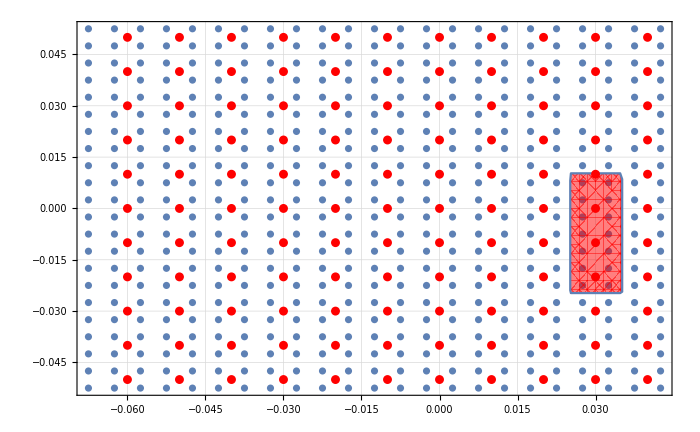

```mathematica
Show[
ListPlot[
Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,2]]-DetHisto[[1,1]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,2]]-DetHisto[[2,1]])/2)-R
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}],1],PlotRange->All],
RegionPlot[Abs[x-ApertXOff]<ApertX/2&&Abs[y+ApertYOff]<ApertY/2,{x,0,0.06},{y,-0.05,0.05},PlotStyle->Directive[Red,Opacity[0.5]]],
ListPlot[XYBinCentersHalf,PlotStyle->Red]
]
```

### we can directly get a XYBin form from original table, even being able to jump over steps by 2 e.g.

```mathematica
XYBinBoundariesOriginal=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+1]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];
```

```mathematica
XYBinBoundariesOriginal//Length
```

506

```mathematica
XYBinBoundariesOriginal[[1]]
```

{{-0.07,-0.065},{0.05,0.055}}

```mathematica
XYBinBoundariesOriginal[[2]]
```

{{-0.07,-0.065},{0.045,0.05}}

### half bins

```mathematica
XYBinBoundariesHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+2]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,2,Length[DetHisto[[1]]]-2,2},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

### we start for x at index 2 for shift, also because that area is 0 anyway

```mathematica
XYBinBoundariesHalf//Length
```

121

```mathematica
(506-22)/4.
```

121.

```mathematica
XYBinBoundariesHalf[[1]]
```

{{-0.065,-0.055},{0.045,0.055}}

### now we still have to adopt the MC data to half binning

### sum the next neighbouring entries

```mathematica
XYBinCentersHalf=BinCenters[XYBinBoundariesHalf];
```

```mathematica
DetHisto[[2+10,5]]+DetHisto[[2+10+1,5]]+DetHisto[[2+10,6]]+DetHisto[[2+10+1,6]]
```

15823

```mathematica
DetHistoBinHalfEntries=Flatten[Table[

DetHisto[[2+xi,yj]]+DetHisto[[2+xi,yj+1]]+DetHisto[[2+xi+1,yj]]+DetHisto[[2+xi+1,yj+1]],
{xi,2,Length[DetHisto[[1]]]-2,2},
{yj,1,Length[DetHisto[[2]]]-2,2}],1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,2,40,119,142,126,75,13,0,0,0,0,108,796,1846,2370,2057,1208,321,17,0,0,4,666,4796,12351,15200,13717,8107,2318,159,0,0,2,1877,15823,50672,62798,58277,33986,7254,455,0,0,2,2377,32479,119667,146391,140010,82674,13509,362,0,0,0,965,38633,175070,210254,207450,121204,13181,47,0,0,0,35,25350,161013,186172,189699,111325,5414,0,0,0,0,0,7093,76815,84945,88555,52117,443,0,0,0,0,0,386,9415,9711,10374,6182,0,0,0,0,0,0,0,4,1,1,5,0,0,0,0}

```mathematica
ListPlot3D[Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]}],PlotRange->All]
```

-Graphics3D-

```mathematica
Show[

ListPlot3D[{#[[1]],#[[2]],#[[3]]/Total[DetTable[[All,3]]]}&/@DetTable,PlotRange->All,PlotStyle->Directive[Opacity[0.5],Red],InterpolationOrder->1],

ListPlot3D[Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]/3.9}],PlotRange->All,InterpolationOrder->1,PlotStyle->Directive[Opacity[0.5],Blue]]
]
```

-Graphics3D-

```mathematica
YDetShift
```

0.015928

```mathematica
Total[DetHistoBinHalfEntries]
```

2627032

```mathematica
Length[DetHistoBinHalfEntries]
```

121

### import other parameters

```mathematica
{{ApertXOff,ApertYOff},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}=Import[MCFolder<>"GlobalTransferData/"<>"OtherParas.txt","Table"]
```

{{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}}

```mathematica
rF=BF/BDV
rA=BA/BDV
rRxB=BRxB/BDV
rDet=BDet/BRxB
```

2.04214

0.994887

0.994674

0.945816

### grab alpha from blines

```mathematica
AlphaFromBlines=178.20869281586448/180*Pi
```

3.11033

```mathematica
(*YBlineShiftatDet=-0.016078000000000037;*)
```

```mathematica
BRxBCenterFromBLines=0.21957007943037976;
```

```mathematica
(BRxBCenterFromBLines-BRxB)/BRxBCenterFromBLines
```

-0.000691704

```mathematica
XAShift=0.0
```

0.

```mathematica
YAShift=0.007188045691239971
```

0.00718805

### we take the “on-top” value

```mathematica
YRxBShift=0.00677284727516161
```

0.00677285

```mathematica
YDetShift=0.015928000000000164
```

0.015928

```mathematica
XRxBShift=0.;
```

```mathematica
XDetShift=0.;
```

### difference is 7e-4. as the MC value is the average over all particles, it doesnt represent the model description. Model needs BRxB in geometric center of beam (actually geometric tube)

### actually, thDet is also different due to alpha not doing 180°!

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

```mathematica
ApertYOff=ApertYOff-R
```

0.00723273

### also, we havent considered a shift at detector due to field lines shifting..

# Get b0 from raw energy fit

```mathematica
Get["NeutronBeam/ManualShift_NBeamInt.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
EHisto={{0,19550,39100,58650,78200,97750,117300,136850,156400,175950,195500,215050,234600,254150,273700,293250,312800,332350,351900,371450,391000,410550,430100,449650,469200,488750,508300,527850,547400,566950,586500,606050,625600,645150,664700,684250,703800,723350,742900,762450,782000},{346513,594262,752207,876257,976772,1057642,1125859,1180669,1225108,1257819,1280816,1294590,1300669,1294235,1281846,1262522,1235139,1200930,1159120,1116025,1064817,1009259,948177,884889,817021,747223,679132,606469,536427,465628,396264,329609,266697,208156,153816,107114,66949,35323,13249,1940}}
```

{{0,19550,39100,58650,78200,97750,117300,136850,156400,175950,195500,215050,234600,254150,273700,293250,312800,332350,351900,371450,391000,410550,430100,449650,469200,488750,508300,527850,547400,566950,586500,606050,625600,645150,664700,684250,703800,723350,742900,762450,782000},{346513,594262,752207,876257,976772,1057642,1125859,1180669,1225108,1257819,1280816,1294590,1300669,1294235,1281846,1262522,1235139,1200930,1159120,1116025,1064817,1009259,948177,884889,817021,747223,679132,606469,536427,465628,396264,329609,266697,208156,153816,107114,66949,35323,13249,1940}}

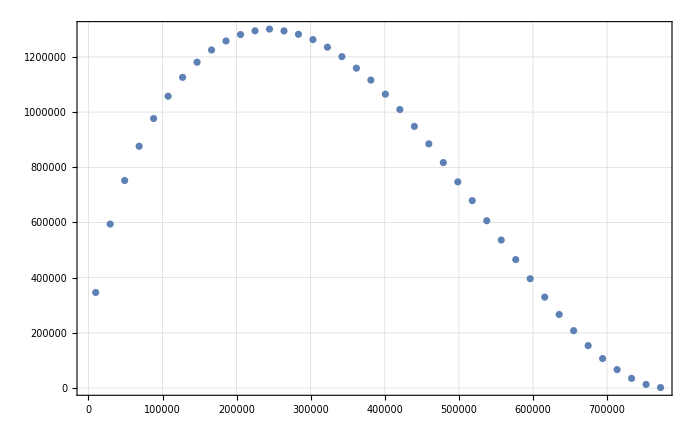

```mathematica
ListPlot[Transpose[{EHisto[[1,1;;-2]]+EHisto[[1,2]]/2,Around[#,Sqrt[#]]&/@EHisto[[2]]}]]
```

```mathematica
FitData=Table[{bin,EHisto[[2,bin]]},{bin,1,Length[EHisto[[2]]]}]
```

{{1,346513},{2,594262},{3,752207},{4,876257},{5,976772},{6,1057642},{7,1125859},{8,1180669},{9,1225108},{10,1257819},{11,1280816},{12,1294590},{13,1300669},{14,1294235},{15,1281846},{16,1262522},{17,1235139},{18,1200930},{19,1159120},{20,1116025},{21,1064817},{22,1009259},{23,948177},{24,884889},{25,817021},{26,747223},{27,679132},{28,606469},{29,536427},{30,465628},{31,396264},{32,329609},{33,266697},{34,208156},{35,153816},{36,107114},{37,66949},{38,35323},{39,13249},{40,1940}}

```mathematica
GlobalStat=Total[EHisto[[2]]]
```

31157159

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,10.4.85.27],KernelObject[2,10.4.85.27],KernelObject[3,10.4.85.27],KernelObject[4,10.4.85.27],KernelObject[5,10.4.85.27],KernelObject[6,10.4.85.27],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local]}

```mathematica
ClearAll[eSpectrumBinned]
```

```mathematica
eSpectrumBinned[b_?NumericQ]:=eSpectrumBinned[b]=GlobalStat*ParallelTable[
NIntegrate[weNormed[λ0,κ0,b,Ee],{Ee,me+EHisto[[1,bin]],me+EHisto[[1,bin+1]]},PrecisionGoal->6],{bin,1,Length[EHisto[[1]]]-1}]
```

```mathematica
ClearAll[eSpectrumBin]
```

```mathematica
eSpectrumBin[b_?NumericQ,bin_?NumericQ]:=eSpectrumBinned[b][[bin]]
```

```mathematica
eSpectrumBin[0.,1]
```

345381.

```mathematica
Total[Table[eSpectrumBin[0.,bin],{bin,1,Length[EHisto[[1]]]-1}]]
```

3.11572×10^7

```mathematica
rawSpecFit=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.6<b<0.6},
{{b,0.5}},
bin,
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.000324095,bin]]

### takes 6 min

```mathematica
rawSpecFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000324095 | 0.00121154 | -0.267506 | 0.790489

### now with statistical weights included

```mathematica
rawSpecFitWeights=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.005<b<0.005},
{{b,0.0001}},
bin,Weights->1/FitData[[All,2]],VarianceEstimatorFunction->(1&),
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.0000338262,bin]]

```mathematica
365/60.
```

6.08333

### takes 6 min

```mathematica
rawSpecFitWeights["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.0000338262 | 0.00134066 | -0.025231 | 0.979999

```mathematica
rawSpecFitWeights["BestFitParameters"][[1,2]]//ScientificForm
```

-3.38262×10^-5

```mathematica
Sqrt[GlobalStat]*0.00134
```

7.47969

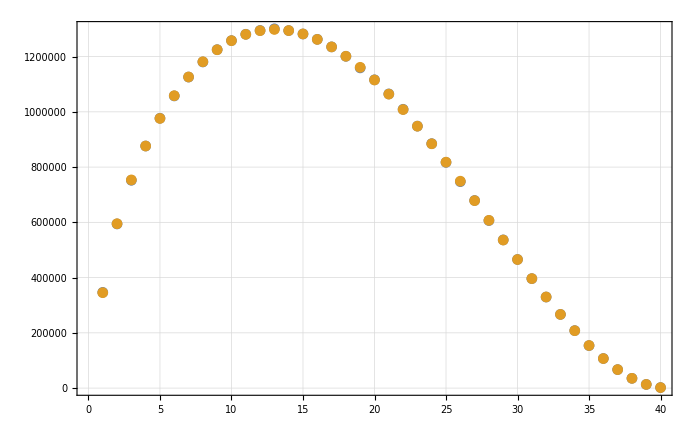

```mathematica
ListPlot[{FitData,Table[rawSpecFitWeights[bin],{bin,1,40}]}]
```

# Get the transfer function

```mathematica
?DeltayDVShift
```

```mathematica
yDofDV[phiDV_,yDV_,p_,th0_,BRxB_,rRxB_,rD_,phiDet_,YDetShift_]=Solve[yDV==DeltayDVShift[phiDV,yD,p,th0,BRxB,rRxB,rD,phiDet,YDetShift],yD][[1,1,2]]
```

(299792458 BRxB rD YDetShift+299792458 BRxB √rD yDV+p rRxB Sin[phiDet] Sin[th0]-p √rD rRxB Sin[phiDV] Sin[th0])/(299792458 BRxB rD)

```mathematica
xDofDV[phiDV_,yDV_,xDV_,p_,th0_,alpha_,BRxB_,rRxB_,rD_,phiDet_,R_,G1_,G2_,{YRxBShift_,XDetShift_,YDetShift_}]=Solve[xDV==DeltaxDV2Shift[phiDV,yDofDV[phiDV,yDV,p,th0,BRxB,rRxB,rD,phiDet,YDetShift],xD,p,th0,alpha,BRxB,rRxB,rD,phiDet,R,G1,G2,{YRxBShift,XDetShift,YDetShift}],xD][[1,1,2]]
```

-1/(√(rD/rRxB) √rRxB)(-√(rD/rRxB) √rRxB XDetShift-xDV-(p √(rD/rRxB) rRxB^(3/2) Cos[phiDet] Sin[th0])/(299792458 BRxB rD)+(p rRxB Cos[phiDV] Sin[th0])/(299792458 BRxB)-(alpha p √rRxB (2-rRxB Sin[th0]^2))/(599584916 √(1-rRxB Sin[th0]^2) (BRxB-(BRxB G1 (YRxBShift+√rD √(1/rRxB) (-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)+(299792458 BRxB rD YDetShift+299792458 BRxB √rD yDV+p rRxB Sin[phiDet] Sin[th0]-p √rD rRxB Sin[phiDV] Sin[th0])/(299792458 BRxB rD))))/R+(BRxB G2 (YRxBShift+√rD √(1/rRxB) (-YDetShift-(p rRxB Sin[phiDet] Sin[th0])/(299792458 BRxB rD)+(299792458 BRxB rD YDetShift+299792458 BRxB √rD yDV+p rRxB Sin[phiDet] Sin[th0]-p √rD rRxB Sin[phiDV] Sin[th0])/(299792458 BRxB rD)))^2)/R^2)))

```mathematica
pmax
```

1.18728×10^6

```mathematica
1.1872848094398074*^6
```

1.18728×10^6

```mathematica
Eofp[1187.28*1000]-me
```

781577.

```mathematica
pmaxlocal=1187.28*1000
```

1.18728×10^6

```mathematica
E0-me
```

781582.

```mathematica
YDetShift
```

0.015928

```mathematica
yDofDV[0.,0.,pmaxlocal,Pi/4,0.2,1,1,0.,YDetShift]
```

0.015928

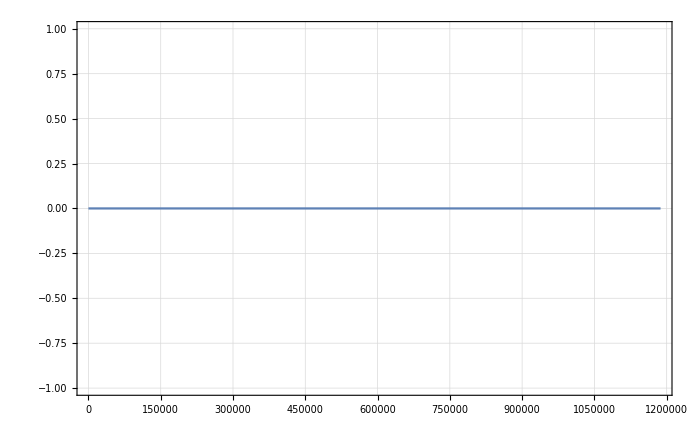

```mathematica
Plot[yDofDV[0.,0.,p,Pi/4,0.2,1,1,0.,0.],{p,0,pmax}]
```

```mathematica
xDofDV[0.,0.,0.,pmaxlocal,0.,Pi,0.2,1.,1.,0.,1,1,1,{0.,0.,0.}]
```

0.0622089

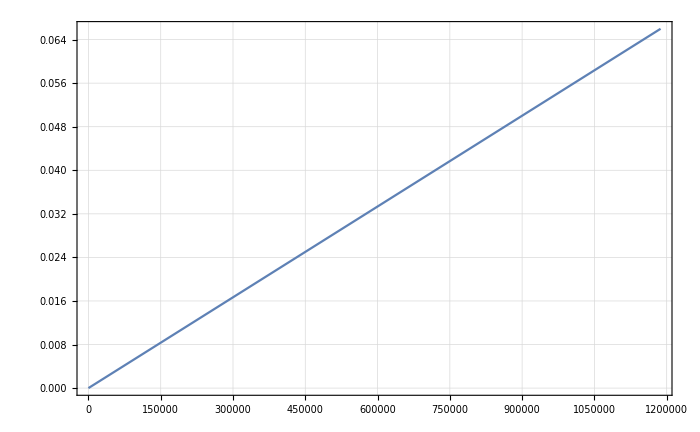

```mathematica
Plot[xDofDV[0.,0.,0.,p,Pi/4,Pi,0.2,1.,1.,0.,1,1,1,{0.,0.,0.}],{p,0,pmax}]
```

### calculate first transfer spectrum with the rough parameters

```mathematica
IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

### calculate bins, choose binsize, multiple of MCData binning

```mathematica
resultfullwShiftPrec44=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf,Method->"FinestGrained"]
```

```mathematica
CloseKernels[]
LaunchKernels[]
```

{}

{KernelObject[1,10.4.85.27],KernelObject[2,10.4.85.27],KernelObject[3,10.4.85.27],KernelObject[4,10.4.85.27],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
ParallelTable[$KernelID,{i,1,20}]
```

{4,4,3,3,2,2,1,1,5,5,6,6,10,10,9,9,8,8,7,7}

```mathematica
NewShiftPrec44Part1=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[1;;24]],Method->"FinestGrained"]
```

{{11.9544,0.},{11.9883,0.},{12.2883,0.},{11.7388,0.},{17.4655,0.},{18.7154,0.},{20.1707,0.},{19.8066,0.},{13.4445,0.},{12.3316,0.},{11.7977,0.},{12.0063,0.},{17.0674,0.},{17.4413,0.},{17.1112,0.},{18.161,0.},{13.2872,0.},{13.3473,0.},{13.4539,0.},{13.5587,0.},{17.6086,0.},{16.5987,0.},{18.4752,0.},{12.2754,0.}}

```mathematica
NewShiftPrec44Part2=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[25;;72]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.0165588,0.00344124}. NIntegrate obtained 0.0489753 and 0.00279973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {-0.00655876,0.00344124}. NIntegrate obtained 0.109479 and 0.00366031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.00344124,0.00344124}. NIntegrate obtained 0.12537 and 0.00344809 for the integral and error estimates.

{{13.9119,0.},{14.0225,0.},{14.4996,0.},{25.9492,1.06491×10^-6},{56.9122,1.26696×10^-6},{54.385,1.29786×10^-6},{60.4172,1.20053×10^-6},{28.4504,0.},{13.7444,0.},{20.9726,0.},{21.2879,0.},{20.8329,0.},{20.9503,0.},{49.7084,9.20807×10^-7},{1152.88,0.00537795},{1000.11,0.00888774},{983.141,0.00916201},{1284.1,0.00883362},{601.551,0.000327576},{28.2846,0.},{35.9123,0.},{36.808,0.},{35.2709,0.},{37.0515,0.},{576.88,0.000548265},{3239.36,0.0489753},{1812.29,0.0818134},{1427.57,0.0840744},{3400.,0.0769682},{1225.48,0.00687423},{26.1987,0.},{26.5538,0.},{26.7139,0.},{26.6502,0.},{26.1795,0.},{1133.26,0.00592914},{4315.33,0.109479},{3181.46,0.18487},{2823.9,0.189936},{5797.19,0.162002},{1956.75,0.0260176},{146.319,0.000121382},{27.7391,0.},{27.3193,0.},{28.0887,0.},{102.069,0.0000728114},{2021.8,0.0150299},{6162.15,0.12537}}

```mathematica
NewShiftPrec44Part3=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[73;;80]],Method->"FinestGrained"]
```

{{5119.52,0.209548},{3940.97,0.215695},{5436.16,0.173068},{2940.13,0.0392326},{845.184,0.00137971},{42.8954,0.},{39.2708,0.},{40.7904,0.}}

```mathematica
NewShiftPrec44Part4=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[81;;88]],Method->"FinestGrained"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in yD near {xD,yD} = {0.0134412,0.00344124}. NIntegrate obtained 0.0889273 and 0.00196924 for the integral and error estimates.

{{459.671,0.000494411},{2747.68,0.0159734},{3724.81,0.0889273},{5304.7,0.144612},{7562.09,0.147921},{7417.46,0.114134},{4500.16,0.0309589},{2621.5,0.00270464}}

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[1,10.4.85.27,<defunct>],KernelObject[2,10.4.85.27,<defunct>],KernelObject[3,10.4.85.27,<defunct>],KernelObject[4,10.4.85.27,<defunct>],KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>],KernelObject[7,local,<defunct>],KernelObject[8,local,<defunct>]}

{KernelObject[9,10.4.85.27],KernelObject[10,10.4.85.27],KernelObject[11,10.4.85.27],KernelObject[12,10.4.85.27],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local]}

```mathematica
NewShiftPrec44Part5=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,XRxBShift, YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf[[89;;-1]],Method->"FinestGrained"]
```

{{26.6112,0.},{26.5619,0.},{24.4743,0.},{917.929,0.000606401},{2670.04,0.00899406},{3647.5,0.0387247},{5499.87,0.0610128},{5353.83,0.0613521},{4112.86,0.0452841},{2233.58,0.0143002},{1372.09,0.00181596},{21.8835,0.},{20.639,0.},{19.5283,0.},{509.343,0.000242937},{1315.18,0.0029055},{3283.46,0.00975262},{3218.25,0.0149313},{3357.54,0.0148346},{3143.01,0.0103664},{1847.43,0.00387439},{766.526,0.000535277},{17.1342,0.},{16.9018,0.},{15.7796,0.},{70.2561,3.33475×10^-6},{858.285,0.000481345},{2542.67,0.00154758},{1995.19,0.00232983},{2001.96,0.00226267},{1919.78,0.00152334},{1517.24,0.000559363},{293.751,0.000039496}}

```mathematica
NewShiftPrec44=Join[NewShiftPrec44Part1,NewShiftPrec44Part2,NewShiftPrec44Part3,NewShiftPrec44Part4,NewShiftPrec44Part5];
```

```mathematica
Total[NewShiftPrec44[[All,1]]]/8/3600
```

5.3087

### so for 8 cores, roughly 5.3 h

```mathematica
ListPlot3D[
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],NewShiftPrec44[[All,2]]/Total[NewShiftPrec44[[All,2]]]}],PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
YDetShift
```

0.015928

### new try with new definition of shifts, not relative shifts used

```mathematica
ApertXOff
```

0.0301277

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[1,10.4.85.27,<defunct>],KernelObject[2,10.4.85.27,<defunct>],KernelObject[3,10.4.85.27,<defunct>],KernelObject[4,10.4.85.27,<defunct>],KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>],KernelObject[7,local,<defunct>],KernelObject[8,local,<defunct>]}

{KernelObject[9,10.4.85.27],KernelObject[10,10.4.85.27],KernelObject[11,10.4.85.27],KernelObject[12,10.4.85.27],KernelObject[13,10.4.85.27],KernelObject[14,10.4.85.27],KernelObject[15,local],KernelObject[16,local],KernelObject[17,local],KernelObject[18,local]}

```mathematica
resultfullwShiftPrec44=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,-ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesHalf,Method->"FinestGrained"]
```

{{12.3367,0.},{12.7676,0.},{13.8309,0.},{13.384,0.},{13.4954,0.},{13.6134,0.},{18.5861,0.},{16.7631,0.},{16.5541,0.},{16.9664,0.},{12.0911,0.},{12.1317,0.},{12.7181,0.},{13.3773,0.},{13.2739,0.},{13.3104,0.},{19.2126,0.},{16.5312,0.},{16.9403,0.},{16.7782,0.},{12.1765,0.},{12.0752,0.},{14.0672,0.},{14.4689,0.},{31.3523,1.60324×10^-6},{46.4639,1.90849×10^-6},{61.5432,1.95623×10^-6},{51.7046,1.71995×10^-6},{20.0316,0.},{19.706,0.},{14.0114,0.},{13.9382,0.},{13.8602,0.},{21.1155,0.},{439.853,0.000105867},{1428.51,0.00789517},{986.731,0.00916814},{1284.9,0.00944929},{1598.59,0.00680035},{182.115,6.62219×10^-6},{21.317,0.},{21.1195,0.},{21.3185,0.},{27.2338,0.},{26.108,0.},{1210.5,0.00377298},{2494.49,0.0680138},{1352.07,0.0822507},{1181.72,0.0844498},{3143.95,0.0591453},{799.676,0.00131406},{26.0982,0.},{25.986,0.},{26.3773,0.},{26.1825,0.},{42.3401,9.5809×10^-6},{2079.47,0.0175541},{4528.27,0.146053},{2396.22,0.18589},{3363.27,0.188216},{6423.76,0.125993},{1769.25,0.00976371},{41.0671,0.},{26.7076,0.},{26.4456,0.},{26.4072,0.},{275.936,0.000618523},{3816.08,0.0309395},{4656.5,0.162673},{4059.32,0.213677},{5741.85,0.21101},{5383.31,0.137446},{2681.44,0.0198995},{247.49,0.000207809},{26.9967,0.},{27.0701,0.},{27.0362,0.},{1005.35,0.00185765},{3873.81,0.0278821},{5097.45,0.11367},{8109.78,0.14947},{5507.32,0.143886},{4980.95,0.0925082},{3121.33,0.0182374},{805.041,0.000887579},{26.8589,0.},{26.5909,0.},{26.3926,0.},{1255.38,0.00164528},{2480.82,0.014615},{4685.8,0.04901},{5378.65,0.0638958},{5174.87,0.0597852},{5018.48,0.0375863},{1973.77,0.009189},{1037.96,0.00075764},{32.3322,0.},{30.9168,0.},{29.5657,0.},{939.923,0.000622621},{1563.4,0.00452408},{2724.25,0.0121066},{3959.35,0.015906},{2690.85,0.0144663},{2269.45,0.00884907},{1169.9,0.00265349},{674.375,0.000216072},{19.8189,0.},{20.6234,0.},{19.0222,0.},{303.39,0.0000631433},{831.171,0.000776553},{1744.93,0.00192613},{1657.44,0.00251496},{2425.59,0.00222572},{1988.81,0.0013123},{794.782,0.000374261},{36.0319,2.61733×10^-6},{9.52256,0.},{9.59619,0.},{9.45761,0.}}

### took 16000s, 4.45h

### time consumption

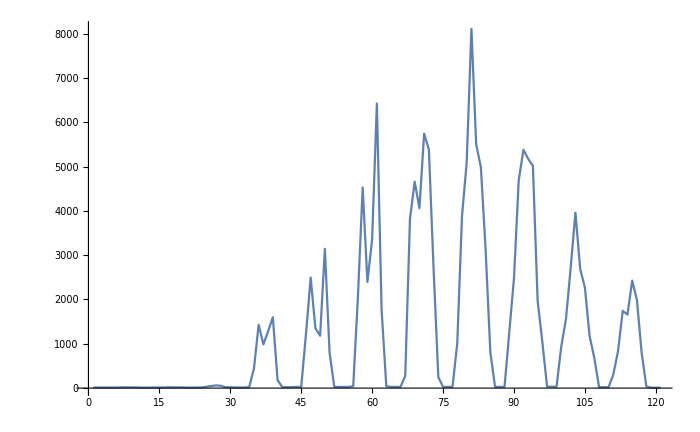

```mathematica
ListLinePlot[resultfullwShiftPrec44[[All,1]]]
```

```mathematica
ListPlot3D[
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec44[[All,1]]}],PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

### result

```mathematica
ListPlot3D[
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec44[[All,2]]/Total[resultfullwShiftPrec44[[All,2]]]}],PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
ListPlot3D[
{Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec44[[All,2]]/Total[resultfullwShiftPrec44[[All,2]]]}],
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]}]
},PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[]
```

```mathematica
Show[
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2)-R,
DetHisto[[2+i,j]]/Total[DetTable[[All,3]]]
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All,PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPlot3D[
Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],resultfullwShiftPrec44[[All,2]]/Total[resultfullwShiftPrec44[[All,2]]]}],PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
]
```

-Graphics3D-

### with original bin size

```mathematica
CloseKernels[]
LaunchKernels[]
```

{KernelObject[9,10.4.85.27,<defunct>],KernelObject[10,10.4.85.27,<defunct>],KernelObject[11,10.4.85.27,<defunct>],KernelObject[12,10.4.85.27,<defunct>],KernelObject[13,10.4.85.27,<defunct>],KernelObject[14,10.4.85.27,<defunct>],KernelObject[15,local,<defunct>],KernelObject[16,local,<defunct>],KernelObject[17,local,<defunct>],KernelObject[18,local,<defunct>]}

{KernelObject[19,10.4.85.27],KernelObject[20,10.4.85.27],KernelObject[21,10.4.85.27],KernelObject[22,10.4.85.27],KernelObject[23,local],KernelObject[24,local],KernelObject[25,local],KernelObject[26,local]}

```mathematica
{XAShift,YAShift,YRxBShift,XDetShift,YDetShift}
```

{0.,0.00718805,0.00677285,0.,0.015928}

```mathematica
resultfullwShiftPrec44OriginalBins=ParallelMap[AbsoluteTiming[BinIntShift[0.,#,{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,-ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal,Method->"FinestGrained"]
```

{{12.6176,0.},{12.9153,0.},{12.5798,0.},{13.0927,0.},{19.3644,0.},{19.306,0.},{20.0209,0.},{18.6237,0.},{13.2841,0.},{13.5859,0.},{13.6385,0.},{13.709,0.},{16.9877,0.},{17.4555,0.},{16.9396,0.},{16.4414,0.},{12.362,0.},{12.5283,0.},{12.475,0.},{12.5536,0.},{16.5164,0.},{16.6685,0.},{16.6116,0.},{17.6891,0.},{12.6623,0.},{13.5461,0.},{14.2595,0.},{13.9208,0.},{13.772,0.},{18.9835,0.},{13.9718,0.},{19.5402,0.},{19.3325,0.},{14.1583,0.},{13.4715,0.},{17.1319,0.},{12.5861,0.},{12.5403,0.},{12.5746,0.},{12.6845,0.},{17.5613,0.},{17.3145,0.},{16.9483,0.},{17.5481,0.},{12.478,0.},{12.7612,0.},{13.1116,0.},{13.4882,0.},{19.4383,0.},{18.6355,0.},{18.244,0.},{13.8432,0.},{19.4194,0.},{14.0307,0.},{14.3516,0.},{14.1399,0.},{13.3432,0.},{12.8507,0.},{12.8301,0.},{16.4022,0.},{17.8591,0.},{12.8827,0.},{16.8261,0.},{17.4891,0.},{12.3208,0.},{12.651,0.},{12.6937,0.},{12.6727,0.},{18.3412,0.},{17.7454,0.},{19.154,0.},{19.5185,0.},{14.0403,0.},{13.8932,0.},{14.0707,0.},{13.8683,0.},{18.9178,0.},{19.6143,0.},{13.268,0.},{17.4405,0.},{12.6526,0.},{17.1459,0.},{12.6288,0.},{12.7487,0.},{12.5631,0.},{12.6529,0.},{12.8245,0.},{12.6894,0.},{18.0164,0.},{16.7531,0.},{16.949,0.},{19.2425,0.},{14.3024,0.},{14.0626,0.},{14.0812,0.},{13.8876,0.},{18.6369,0.},{19.7903,0.},{18.4167,0.},{19.0832,0.},{13.3693,0.},{13.0209,0.},{12.748,0.},{12.6971,0.},{12.5725,0.},{17.4516,0.},{16.4028,0.},{12.7198,0.},{18.1734,0.},{12.8941,0.},{12.8651,0.},{17.1154,0.},{12.801,0.},{13.6724,0.},{14.4755,0.},{14.1688,0.},{18.7358,0.},{19.4325,0.},{18.8229,0.},{18.686,0.},{13.9507,0.},{14.0395,0.},{13.4045,0.},{12.7934,0.},{17.6228,0.},{17.0458,0.},{17.7357,0.},{12.4586,0.},{16.8296,0.},{12.8488,0.},{12.8417,0.},{12.693,0.},{14.9006,0.},{20.5837,0.},{15.4074,0.},{20.4541,0.},{32.9946,6.1934×10^-7},{49.1629,7.71448×10^-7},{66.9382,7.80962×10^-7},{63.201,7.90664×10^-7},{48.2048,8.00559×10^-7},{48.8315,8.10649×10^-7},{66.2156,8.20938×10^-7},{41.7123,1.55265×10^-7},{15.7011,0.},{15.2537,0.},{15.1507,0.},{15.1937,0.},{20.9874,0.},{15.1814,0.},{15.2648,0.},{15.3367,0.},{19.9961,0.},{20.5717,0.},{19.9603,0.},{20.7993,0.},{20.6842,0.},{199.866,1.51365×10^-6},{1890.35,0.000344122},{1024.6,0.000450593},{1034.55,0.000457398},{1046.59,0.000464352},{823.592,0.000471459},{849.452,0.000478722},{1006.38,0.000486032},{1370.04,0.000192201},{20.0516,0.},{19.9719,0.},{20.4802,0.},{19.8407,0.},{20.4448,0.},{19.7152,0.},{20.3773,0.},{20.0005,0.},{20.4109,0.},{19.9421,0.},{21.5661,0.},{21.8039,0.},{21.7429,0.},{814.543,0.000106867},{2517.44,0.00300326},{1445.63,0.0040315},{1649.16,0.00409234},{1664.37,0.00415421},{1669.86,0.00421738},{1314.1,0.00428189},{1866.44,0.00430803},{3018.39,0.00176459},{254.957,6.78845×10^-6},{28.8321,0.},{29.4145,0.},{27.2145,0.},{28.136,0.},{21.7404,0.},{28.479,0.},{27.6987,0.},{21.7586,0.},{28.2226,0.},{34.7591,0.},{33.9461,0.},{41.5802,4.33121×10^-7},{1824.18,0.000835562},{3734.92,0.00953792},{2133.35,0.0133111},{965.961,0.013548},{978.3,0.0137418},{992.121,0.0139394},{965.571,0.0141407},{2971.91,0.0138527},{2850.86,0.00601975},{717.191,0.00018983},{34.0112,0.},{26.2154,0.},{34.7526,0.},{26.2595,0.},{34.3711,0.},{26.2148,0.},{26.1813,0.},{33.9316,0.},{26.0932,0.},{33.7156,0.},{26.1806,0.},{339.155,0.0000415734},{2193.13,0.00289561},{3768.7,0.0184049},{3374.71,0.026496},{1347.57,0.0273049},{1074.98,0.0276557},{1064.24,0.0280121},{1665.9,0.0283535},{4219.36,0.0266501},{3367.36,0.0124276},{1704.53,0.00111883},{56.3797,1.54315×10^-6},{26.3536,0.},{26.1311,0.},{26.0731,0.},{26.2527,0.},{26.2254,0.},{26.0319,0.},{26.2422,0.},{26.0466,0.},{26.3824,0.},{26.5517,0.},{714.171,0.000389967},{2406.31,0.00619305},{4592.51,0.0268189},{5077.87,0.0390652},{2772.76,0.0412046},{1718.98,0.0416644},{2314.22,0.0421107},{2975.19,0.042301},{3671.29,0.0380598},{3682.91,0.0190027},{2645.78,0.00321645},{401.08,0.00011031},{35.316,0.},{33.7139,0.},{35.7045,0.},{35.7718,0.},{35.1183,0.},{34.499,0.},{36.682,0.},{34.2496,0.},{36.1138,0.},{95.4862,0.0000176248},{1889.62,0.00137417},{4541.47,0.00961998},{5411.55,0.0326397},{5379.,0.0472515},{3574.91,0.0512124},{2437.44,0.0518172},{2546.15,0.0522139},{3918.95,0.0515896},{5533.96,0.044949},{5264.08,0.0237763},{2962.08,0.00583698},{1071.83,0.000581271},{54.6991,0.},{35.687,0.},{37.4079,0.},{37.1724,0.},{35.742,0.},{36.8635,0.},{36.7054,0.},{35.5282,0.},{36.7068,0.},{350.362,0.000154748},{2746.96,0.00273501},{4091.98,0.0119608},{4517.8,0.034609},{5254.43,0.0494391},{4528.6,0.0546261},{3338.45,0.0555892},{3152.2,0.0557301},{6654.51,0.0538434},{6968.61,0.0460862},{6084.49,0.0254412},{3107.86,0.00781578},{1778.92,0.0014471},{141.709,0.0000327319},{25.6201,0.},{25.6473,0.},{26.1119,0.},{25.8061,0.},{26.0529,0.},{25.5792,0.},{26.3846,0.},{39.7646,6.12239×10^-7},{932.078,0.000463677},{2521.74,0.00378418},{3201.43,0.0125325},{5038.01,0.0325367},{8835.89,0.0457948},{5946.83,0.0510419},{3136.72,0.0524099},{4325.69,0.0521132},{7719.29,0.0493319},{7824.84,0.0418746},{5923.02,0.0238148},{3461.86,0.00840357},{2465.5,0.00223693},{482.457,0.000176705},{26.0891,0.},{26.4816,0.},{26.692,0.},{26.0934,0.},{26.2497,0.},{26.3542,0.},{25.5951,0.},{102.177,0.0000168492},{1502.24,0.000820422},{3084.47,0.00404517},{2713.46,0.0113176},{4994.17,0.0272807},{6858.67,0.0378891},{7917.83,0.042299},{6376.45,0.0437283},{4854.25,0.0430797},{8062.68,0.0401873},{5986.83,0.0338909},{5181.66,0.0196954},{3142.2,0.00761488},{2637.77,0.00248365},{1012.82,0.000381317},{80.2925,4.28105×10^-6},{24.9923,0.},{25.2819,0.},{25.4528,0.},{25.4839,0.},{25.569,0.},{35.1294,0.},{333.106,0.0000665167},{2566.66,0.000959347},{2722.61,0.00354943},{2845.69,0.00898971},{6385.82,0.0203508},{4681.14,0.0279396},{7896.24,0.0311748},{6312.42,0.0322711},{7386.44,0.0315417},{6519.4,0.0291142},{4897.86,0.0243189},{3816.24,0.0144068},{3012.11,0.00598257},{3416.79,0.00218445},{1393.63,0.00047327},{260.076,0.0000171722},{24.8805,0.},{24.5994,0.},{24.3579,0.},{24.5463,0.},{24.3587,0.},{24.5303,0.},{698.205,0.000105268},{2122.59,0.000843671},{2155.66,0.00268754},{2847.42,0.00628273},{4947.56,0.0133166},{3755.27,0.0180818},{5135.4,0.0201829},{7337.73,0.0208429},{4246.23,0.0202213},{5178.87,0.0184036},{4783.03,0.0151755},{3121.39,0.0092132},{2727.25,0.00410464},{2859.98,0.00160783},{1986.06,0.000415575},{361.972,0.0000260289},{24.1944,0.},{24.3657,0.},{23.0615,0.},{22.8187,0.},{23.3185,0.},{22.6104,0.},{1111.55,0.000103271},{1447.58,0.000598464},{2013.28,0.00175686},{1645.14,0.00386841},{4078.99,0.00748761},{3731.86,0.0100493},{3645.25,0.0112617},{6954.57,0.0116088},{4792.3,0.0111628},{3090.62,0.00999875},{3731.5,0.00807877},{1831.09,0.00508185},{1816.15,0.00246674},{1646.69,0.00101126},{1780.62,0.000283239},{507.742,0.0000270803},{20.1146,0.},{19.8024,0.},{19.6773,0.},{19.6488,0.},{19.4161,0.},{19.427,0.},{645.825,0.0000645616},{1113.81,0.000354344},{2020.39,0.000998988},{1638.25,0.00207967},{1699.5,0.00362536},{2802.35,0.00481667},{3846.05,0.00544688},{4790.99,0.00562205},{3295.15,0.00536681},{2940.06,0.0047288},{2409.4,0.00374505},{2473.26,0.00245114},{1972.89,0.0012885},{1099.92,0.000542794},{941.79,0.000154015},{299.514,0.0000140506},{25.22,0.},{17.2783,0.},{23.8492,0.},{16.377,0.},{15.5984,0.},{22.3897,0.},{467.944,0.0000275471},{1198.06,0.000172916},{1490.99,0.000482237},{1709.93,0.00097548},{2023.05,0.001579},{2707.08,0.00208299},{2215.76,0.00237837},{3203.07,0.00245976},{3793.53,0.00233699},{2691.24,0.00203524},{2820.63,0.00159188},{2537.54,0.00106186},{1233.25,0.0005766},{874.98,0.000240777},{779.925,0.0000608835},{40.3698,3.36903×10^-7},{11.423,0.},{11.1658,0.},{10.94,0.},{10.8155,0.},{10.6873,0.},{10.6839,0.},{45.6757,4.59167×10^-7},{394.068,0.0000468824},{690.794,0.000193927},{1753.54,0.000393916},{2439.39,0.00062574},{2479.05,0.000822365},{1610.81,0.000938051},{2321.29,0.000963259},{2859.38,0.000908081},{1836.72,0.000784781},{2834.48,0.000606956},{2964.88,0.000401375},{1183.69,0.000214503},{698.26,0.0000818902},{49.4058,7.11477×10^-7},{9.61524,0.},{9.68088,0.},{9.47264,0.},{14.1339,0.},{9.55402,0.},{13.7569,0.},{9.39925,0.},{9.38422,0.},{312.98,7.56655×10^-6},{713.838,0.0000607369},{1198.97,0.000128662},{2202.12,0.000206821},{1683.97,0.000271406},{1704.4,0.00030573},{1942.88,0.000308448},{2480.34,0.000286926},{2415.51,0.00024592},{1650.76,0.000187345},{1910.23,0.000120294},{1019.81,0.0000607991},{493.561,0.0000202873},{13.3988,0.},{13.8262,0.},{13.2208,0.},{13.833,0.},{13.7518,0.},{12.8417,0.},{12.8228,0.},{13.272,0.}}

### took 75855s

```mathematica
XYBinCentersOriginal=BinCenters[XYBinBoundariesOriginal];
```

```mathematica
Show[
ListPlot3D[
Transpose[{XYBinCentersOriginal[[All,1]],XYBinCentersOriginal[[All,2]],resultfullwShiftPrec44OriginalBins[[All,2]]/Total[resultfullwShiftPrec44OriginalBins[[All,2]]]}],
PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]],

ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2)-R,
DetHisto[[2+i,j]]/Total[DetTable[[All,3]]]
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All,PlotStyle->Directive[Blue,Opacity[0.5]]]
]
```

-Graphics3D-